```mathematica
Manipulate[Plot[b Cos[theta] + a (Sin[theta])^2, {theta, 0, Pi}], {a, -5, 5}, {b, -5,5}]
```

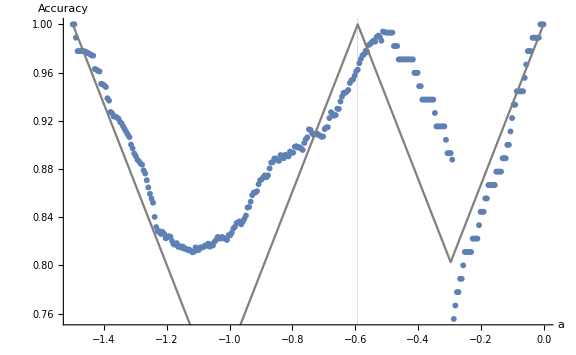

```mathematica
path = "/home/koritskiy/rqc/ferrimagnet/confusion_learning/results/hysteresis/2020-08-13-18:17:44/";
A =Transpose[Import[StringJoin[path , "A.dat"]]][[1]];
b = Transpose[Import[StringJoin[path , "b.dat"]]][[1]];
Z =Flatten[Import[StringJoin[path , "Z.dat"]]];
c =Import[StringJoin[path , "C.dat"]][[1]][[1]];
Znearest = Flatten[Import[StringJoin[path , "Z_nearest.dat"]]];
result = ListPlot[
Table[{A[[i]], Z[[i]]}, {i, 1, Length[A]}],
AxesLabel->{"a", "Accuracy"},
PlotLegends->Automatic,
ImageSize->Large];
closest = ListLinePlot[
Table[{A[[i]], Znearest[[i]]}, {i, 1, Length[A]}],
AxesLabel->{"a", "Accuracy"},
PlotStyle->Gray,
PlotLegends->Automatic,
ImageSize->Large];
Show[result, closest, 
GridLines->{{c},{}}]
```

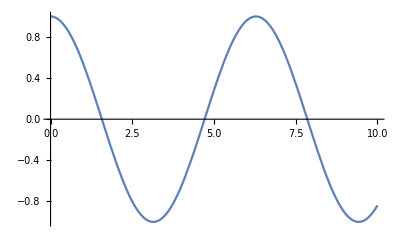

```mathematica
Plot[Cos[x],{x,0,10},GridLines->{{Pi} ,{}}]
```